```mathematica
(* This file looks at some excluded volume algorithms. *)
```

```mathematica
(*************************)
(* Define some functions *)
(*************************)
```

```mathematica
(* Gaussian *)
gauss[x_,sigma_]:=1/(sigma*Sqrt[2*Pi])*Exp[-x^2/(2*sigma^2)]
```

```mathematica
(* Produces a random gaussian deviate centered at 0 with std. dev. sigma *)
randomvect[sigma_]:=RandomVariate[MultinormalDistribution[{0,0,0},{{sigma^2,0,0},{0,sigma^2,0},{0,0,sigma^2}}]]
```

```mathematica
(* Bounces a molecule starting from xvect for a unit sphere about origin *)
bounce[xvect_]:=Module[{dist},
dist=Norm[xvect];
If[dist<1,(1+(1-dist))*xvect/dist,xvect]]
```

```mathematica
(* Diffuse with constraint *)
diffusenearsphere[xvect_,nsteps_,steplength_]:=Module[{pos},
pos=xvect;
For[i=1,i≤nsteps,i++,pos=bounce[pos+randomvect[steplength]]];
Return[pos];]
```

```mathematica
(* Reflect correctly off of a sphere *)
reflectoffsphere[rvect_,svect_]:=Module[{a,b,c,p,xvect,yvect},
yvect=If[Norm[svect]>=1,svect,
a=(svect-rvect).(svect-rvect);
b=2*rvect.(svect-rvect);
c=rvect.rvect-1;
p=(-b-Sqrt[b^2-4*a*c])/(2*a);
xvect=(1-p)*rvect+p*svect;
xvect+(svect-xvect)-2*(svect-xvect).xvect*xvect];
Return[yvect];]
```

```mathematica
(* Diffuse with sphere constraint, now using reflection algorithm. *)
diffusenearsphere2[xvect_,nsteps_,steplength_]:=Module[{pos},
pos=xvect;
For[i=1,i≤nsteps,i++,pos=reflectoffsphere[pos,pos+randomvect[steplength]]];
Return[pos];]
```

```mathematica
(* Converts from x,y,z coordinates to x,z *)
cyl2plane[xvect_]:={Sqrt[xvect[[1]]^2+xvect[[2]]^2],xvect[[3]]}
```

```mathematica
(* Compute polar angle in spherical coordinates for given vector.  This angle is angle away from z axis. *)
computetheta[xvect_]:=ArcTan[xvect[[3]],Sqrt[xvect[[1]]^2+xvect[[2]]^2]]
```

```mathematica
(* Takes a list of values and converts this to a histogram that can be graphed using the given bin width.  Result should integrate to 1. *)
histlist[dist_,binwidth_]:=Module[{hist},
hist=HistogramList[dist,{binwidth}];
hist[[1]]=hist[[1]]-binwidth/2;
hist[[1]]=Drop[hist[[1]],1];
hist[[2]]=hist[[2]]/Total[hist[[2]]]/binwidth;
Return[Transpose[hist]]];
```

```mathematica
(*****************)
(* Test fuctions *)
(*****************)
```

```mathematica
randomvect[1]
```

{0.212825,-0.598603,-1.03557}

```mathematica
bounce[{0.1,0.1,0.1}]
```

{1.0547,1.0547,1.0547}

```mathematica
test=reflectoffsphere[{1.5,0,0},{0.1,0.2,0}]
Norm[test]
```

{1.86722,0.32721,0.}

1.89568

```mathematica
(************************************)
(* Compute distributions for sphere *)
(************************************)
```

```mathematica
(* Sphere has radius 1.  s is rms step length.  binwidth is histogram bin width in radians.  samples is number of random samples. *)
```

```mathematica
s=0.5
posx={0,0,1.1}
binwidth=0.1
samples=100000
```

0.5

{0,0,1.1}

0.1

100000

```mathematica
freedata=Table[posx+randomvect[s],{samples}];
```

```mathematica
onestepdata=Table[diffusenearsphere[posx,1,s],{samples}];
```

```mathematica
multistepdata=Table[diffusenearsphere[posx,20,s/Sqrt[20]],{samples}];
```

```mathematica
onestepdata2=Table[diffusenearsphere2[posx,1,s],{samples}];
```

```mathematica
multistepdata2=Table[diffusenearsphere2[posx,20,s/Sqrt[20]],{samples}];
```

```mathematica
Show[{ListPointPlot3D[onestepdata2,PlotStyle->PointSize[0.001],PlotRange->{{-2,2},{-2,2},{-1,3}}],
Graphics3D[Sphere[{0,0,0}]]},BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
free2d=Table[cyl2plane[freedata[[i]]],{i,samples}];
onestep2d=Table[cyl2plane[onestepdata[[i]]],{i,samples}];
multistep2d=Table[cyl2plane[multistepdata[[i]]],{i,samples}];
onestep2d2=Table[cyl2plane[onestepdata2[[i]]],{i,samples}];
multistep2d2=Table[cyl2plane[multistepdata2[[i]]],{i,samples}];
```

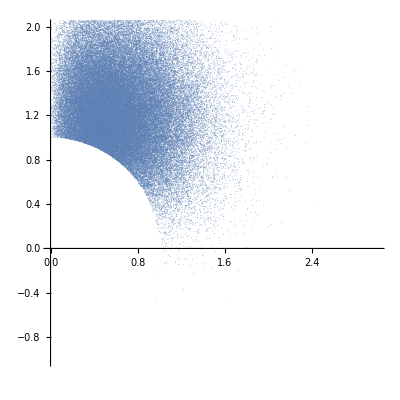

```mathematica
ListPlot[multistep2d2,PlotStyle->PointSize[0.001],PlotRange->{{0,3},{-1,2}},AspectRatio->1]
```

```mathematica
Mean[freedata]
StandardDeviation[freedata]
Skewness[freedata]
```

{0.000287523,0.0000299682,1.09987}

{0.500507,0.50079,0.4997}

{-0.00444761,-0.00183434,0.014355}

```mathematica
Mean[onestepdata]
StandardDeviation[onestepdata]
Skewness[onestepdata]
```

{0.0016674,0.000196558,1.17334}

{0.5539,0.551365,0.457443}

{0.00118144,-0.000149885,-0.395517}

```mathematica
Mean[multistepdata]
StandardDeviation[multistepdata]
Skewness[multistepdata]
```

{-0.000108248,-0.000271175,1.2916}

{0.529829,0.530295,0.385977}

{0.0104291,0.00482582,0.327375}

```mathematica
Mean[onestepdata2]
StandardDeviation[onestepdata2]
Skewness[onestepdata2]
```

{0.00077603,0.00319469,1.30386}

{0.509039,0.509931,0.388463}

{-0.0157499,0.00622991,0.115991}

```mathematica
Mean[multistepdata2]
StandardDeviation[multistepdata2]
Skewness[multistepdata2]
```

{0.000918163,-0.00124984,1.3008}

{0.526588,0.527176,0.382197}

{0.00447287,-0.00711866,0.355783}

```mathematica
freetheta=Table[computetheta[freedata[[i]]],{i,samples}];
onesteptheta=Table[computetheta[onestepdata[[i]]],{i,samples}];
multisteptheta=Table[computetheta[multistepdata[[i]]],{i,samples}];
onesteptheta2=Table[computetheta[onestepdata2[[i]]],{i,samples}];
multisteptheta2=Table[computetheta[multistepdata2[[i]]],{i,samples}];
```

```mathematica
histfreetheta=histlist[freetheta,binwidth];
histonesteptheta=histlist[onesteptheta,binwidth];
histmultisteptheta=histlist[multisteptheta,binwidth];histonesteptheta2=histlist[onesteptheta2,binwidth];
histmultisteptheta2=histlist[multisteptheta2,binwidth];
```

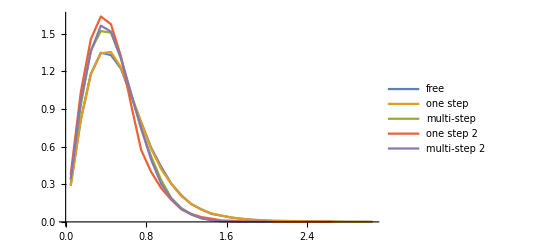

```mathematica
ListLinePlot[{histfreetheta,histonesteptheta,histmultisteptheta,histonesteptheta2,histmultisteptheta2},PlotLegends->{"free","one step","multi-step","one step 2","multi-step 2"}]
```

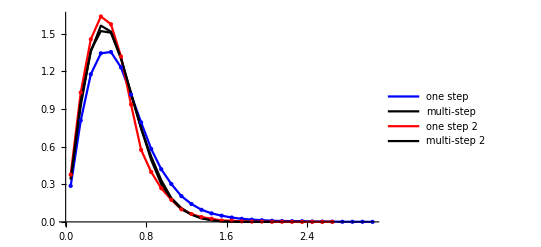

```mathematica
Show[{ListLinePlot[{histonesteptheta,histmultisteptheta,histonesteptheta2,histmultisteptheta2},PlotLegends->{"one step","multi-step","one step 2","multi-step 2"},PlotStyle->{Blue,Black,Red,Black}],
ListPlot[{histonesteptheta,histonesteptheta2},PlotStyle->{Directive[Blue,PointSize[Medium]],Directive[Red,PointSize[Medium]]}]},AxesStyle->Directive[Bold,12]]
```

```mathematica
Mean[freetheta]
Mean[onesteptheta]
Mean[multisteptheta]
Mean[onesteptheta2]
Mean[multisteptheta2]
```

0.56188

0.561817

0.488959

0.469436

0.483295

```mathematica
freeradius=Table[Norm[freedata[[i]]],{i,samples}];
onestepradius=Table[Norm[onestepdata[[i]]],{i,samples}];
multistepradius=Table[Norm[multistepdata[[i]]],{i,samples}];onestepradius2=Table[Norm[onestepdata2[[i]]],{i,samples}];
multistepradius2=Table[Norm[multistepdata2[[i]]],{i,samples}];
```

```mathematica
histfreeradius=histlist[freeradius,binwidth];
histonestepradius=histlist[onestepradius,binwidth];
histmultistepradius=histlist[multistepradius,binwidth];histonestepradius2=histlist[onestepradius2,binwidth];
histmultistepradius2=histlist[multistepradius2,binwidth];
```

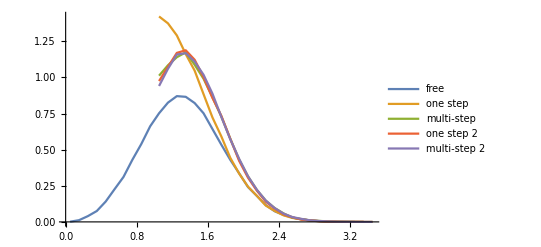

```mathematica
ListLinePlot[{histfreeradius,histonestepradius,histmultistepradius,histonestepradius2,histmultistepradius2},PlotLegends->{"free","one step","multi-step","one step 2","multi-step 2"}]
```

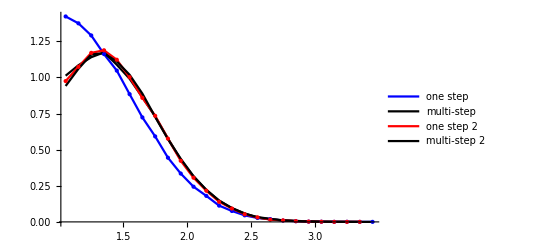

```mathematica
Show[{ListLinePlot[{histonestepradius,histmultistepradius,histonestepradius2,histmultistepradius2},PlotLegends->{"one step","multi-step","one step 2","multi-step 2"},PlotStyle->{Blue,Black,Red,Black}],
ListPlot[{histonestepradius,histonestepradius2},PlotStyle->{Directive[Blue,PointSize[Medium]],Directive[Red,PointSize[Medium]]}]},AxesStyle->Directive[Bold,12]]
```

```mathematica
Mean[freetheta]
Mean[onesteptheta]
Mean[multisteptheta]
Mean[onesteptheta2]
Mean[multisteptheta2]
```

0.56188

0.561817

0.488959

0.469436

0.483295